```mathematica
Quit[]
```

## Set up the Units, Constants and Kinematics:

### General Setup:

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Define Some General Functions:

```mathematica
MTParallelTable[expression_,indexesDescriptors__]:=Module[{tuplesLength,counter1,counter2,printTemporaryCell,tableResult,res},tuplesLength=Length[Tuples[Map[Range[Rest[#]/.List->Sequence]&,{indexesDescriptors}]]];
counter1=0;
counter2=0;
SetSharedVariable[counter1];
SetSharedVariable[counter2];
printTeporaryCell=PrintTemporary[Dynamic[NumberForm[Clock[{0,Infinity}],{Infinity,1}],TrackedSymbols:>{},UpdateInterval->0.01]];
With[{parallelKernelAssumptions=$Assumptions},ParallelEvaluate[$Assumptions=parallelKernelAssumptions]];
tableResult=Monitor[ParallelTable[counter1++;res=expression;counter2++;res,indexesDescriptors],"Running: "<>ToString[counter1]<>"/"<>ToString[tuplesLength]<>", Evaluated: "<>ToString[counter2]<>"/"<>ToString[tuplesLength]];
NotebookDelete[printTemporaryCell];
tableResult]
SetAttributes[MTParallelTable,HoldAll];
```

```mathematica
Clear[Smooth3D];
Smooth3D[table_,newdim_,IntOrder_]:=Module[{dim,smoothtable1,ival,jval,ixarray,jxarray,ixfunc,jxfunc,ivalrange,jvalrange,Δival,Δjval},
dim=table//Dimensions;
smoothtable1=Table[
ival=table[[i,1,1]];
jxarray=table[[i,All,{2,3}]];
jxfunc=Interpolation[jxarray,InterpolationOrder->IntOrder];
jvalrange=jxfunc[[1,1]];
Δjval=(jvalrange[[2]]-jvalrange[[1]])/(newdim[[2]]-1);
Table[{ival,jval,jxfunc[jval]},{jval,jvalrange[[1]],jvalrange[[2]],Δjval}],{i,1,dim[[1]]}];
dim=smoothtable1ᵀ//Dimensions;
Table[
ival=smoothtable1ᵀ[[i,1,2]];
jxarray=smoothtable1ᵀ[[i,All,{1,3}]];
jxfunc=Interpolation[jxarray,InterpolationOrder->IntOrder];
jvalrange=jxfunc[[1,1]];
Δjval=(jvalrange[[2]]-jvalrange[[1]])/(newdim[[2]]-1);
Table[{jval,ival,jxfunc[jval]},{jval,jvalrange[[1]],jvalrange[[2]],Δjval}],{i,1,dim[[1]]}]ᵀ
]
```

```mathematica
Clear[NormPDFfromValList];
NormPDFfromValList[ValList_,binsspecs_]:=Module[{bins,Histvals,binMeans,binΔ,n,PDFdata},
{bins,Histvals}=HistogramList[ValList,binsspecs];
binMeans=Table[Mean[bins[[i;;i+1]]],{i,1,Length[bins]-1}];
binΔ=Table[bins[[i+1]]-bins[[i]],{i,1,Length[bins]-1}];
n=Total[Histvals];
PDFdata={binMeans,Histvals/(n binΔ)}ᵀ
]

Clear[PDFfromValList];
PDFfromValList[ValList_,binsspecs_]:=Module[{bins,Histvals,binMeans,PDFdata},
{bins,Histvals}=HistogramList[ValList,binsspecs];
binMeans=Table[Mean[bins[[i;;i+1]]],{i,1,Length[bins]-1}];
PDFdata={binMeans,Histvals}ᵀ
]

ClearAll[pntToRectPoints]
pntToRectPoints[xy_]:=Module[{x,y,midx,newx},
x=xy[[All,1]];
y=xy[[All,2]];
midx=Table[Mean[x[[i;;i+1]]],{i,1,Length[xy]-1}];
newx=Join[{2 x[[1]]-midx[[1]]},midx,{2x[[-1]]-midx[[-1]]}];
Flatten[Table[{{newx[[j]],y[[j]]},{newx[[j+1]],y[[j]]}},{j,1,Length[newx]-1}],1]
]
```

### Units:

```mathematica
Get["Math Misc/MyUnits.m"]
ClearUnits[];
SetConsts[];

MplMeV=Mpl//InUnits[MeV]//RemoveUnits;
MplGeV=Mpl//InUnits[GeV]//RemoveUnits;

GNewt=1/Mpl^2;
GNewtGeVm2=GNewt//InUnits[GeV^-2]//RemoveUnits;

meMeV=melectron//InUnits[MeV]//RemoveUnits;
mμMeV=mmuon//InUnits[MeV]//RemoveUnits;
mτMeV=mtau//InUnits[MeV]//RemoveUnits;
mπMeV=mpizero//InUnits[MeV]//RemoveUnits;
```

### Stuff for Plots:

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
NiceColor[i_]:=ColorData[97,"ColorList"][[i]]
```

```mathematica
PrettyExp[x_,MAX_:2]:=If[Abs[x]≥MAX,Superscript[10,x],If[x≥0,10^x,10.^x]]

Logticks[Log10min_,Log10max_,AMAX_:1]:=Flatten[Table[Prepend[Flatten[Table[{Log10[i*10.^x],"",{.008,0}},{i,2,9}],{1}],{Log10[10.^x],PrettyExp[x,AMAX],{.02,0}}],{x,Floor[Log10min],Ceiling[Log10max],1}],1]

fontsize=18;
(*plotstyle={Frame->True,Background->White,ImageSize->400,PlotStyle->{{NiceColor[1]}},BaseStyle->{FontFamily->"Times"},FrameStyle->Directive[fontsize,Black,FontFamily->"Times"(*Times*)]};*)
```

```mathematica
plotstyle={FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Black,Black},{Black,Black}},(*PlotRange->All,*)Background->White,ImageSize->400,LabelStyle-> Directive[fontsize,Black,FontFamily->Times],FrameStyle-> Directive[fontsize,Black,FontFamily->Times],Frame->True,(*GridLines->Automatic,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness->0.001], *)Axes->False,AspectRatio->GoldenRatio^-1(*,PlotRangePadding->None*)};
plotstyleSquare={FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Black,Black},{Black,Black}},(*PlotRange->All,*)Background->White,ImageSize->400,LabelStyle-> Directive[fontsize,Black,FontFamily->Times],FrameStyle-> Directive[fontsize,Black,FontFamily->Times],Frame->True,(*GridLines->Automatic,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness->0.001], *)Axes->False,AspectRatio->1,PlotRangePadding->None};
plotstyleSquareSmall={FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Black,Black},{Black,Black}},(*PlotRange->All,*)Background->White,ImageSize->300,LabelStyle-> Directive[fontsize,Black,FontFamily->Times],FrameStyle-> Directive[fontsize,Black,FontFamily->Times],Frame->True,(*GridLines->Automatic,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness->0.001], *)Axes->False,AspectRatio->1,PlotRangePadding->None};
plotstyleSquareSuperSmall={FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Black,Black},{Black,Black}},(*PlotRange->All,*)Background->White,ImageSize->220,LabelStyle-> Directive[12,Black,FontFamily->Times],FrameStyle-> Directive[fontsize,Black,FontFamily->Times],Frame->True,(*GridLines->Automatic,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness->0.001], *)Axes->False,AspectRatio->1,PlotRangePadding->None};
plotstylelog={FrameTicksStyle->{{Black,Black},{Black,Black}},PlotRange->All,Background->White,ImageSize->500,GridLines->Automatic,LabelStyle-> Directive[fontsize,Black,FontFamily->Times],FrameStyle-> Directive[fontsize,Black,FontFamily->Times],Frame->True,GridLinesStyle->Directive[Lighter[Gray,0.8],Thickness->0.001], Axes->False,AspectRatio->GoldenRatio^-1};
```

```mathematica
bluino=RGBColor[0.4,0.52,0.85];
rossino=RGBColor[0.9,0.1,0.1];
giallino=RGBColor[1,0.83,0.01];
verdino=RGBColor[0.15,0.7,0.15];
violino=RGBColor[0.8,0.5,0.85];
```

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{color,txfonts}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

## Inner Slope vs Baryonic Properties:

```mathematica
Clear[αxDC14withErrors];
αxDC14withErrors[x200_,c200_,Δc200_,MsMhvir_,ΔMsMhvir_]:=Module[{X,ΔX,α,Δα,β,Δβ,γ,Δγ,αx,Δαx},
X=Log10[MsMhvir];
ΔX=ΔMsMhvir/(MsMhvir Log[10]);
α=2.94-Log10[(10^(X+2.33))^-1.08+(10^(X+2.33))^2.29];
Δα=(-2.29+1/(0.297+2.111 10^7(10^X)^3.37)) ΔX;
β=4.23+1.34 X+0.26 X^2;
Δβ=(1.34+0.52 X) ΔX;
γ=-0.06+Log10[(10^(X+2.56))^-0.68+10^(X+2.56)];
Δγ=(1+1/(-0.595-11898.5 (10^X)^1.68)) ΔX;
αx=-((x200 c200)^α β+γ)/(1+(x200 c200)^α);
Δαx=√((((c200 x200)^α (β-γ) Log[c200 x200])/((1+(c200 x200)^α)^2)Δα)^2+((1/(1+(c200 x200)^α)-1) Δβ)^2+(Δγ/(1+(c200 x200)^α))^2+(((c200 x200)^α α (β-γ))/(c200 (1+(c200 x200)^α)^2)Δc200)^2);

{αx,Δαx}
]
```

```mathematica
Clear[ρDC14];
ρDC14[ρs_,rrs_,MsMhvir_]:=Module[{X,α,β,γ},
X=Log10[MsMhvir];
α=2.94-Log10[(10^(X+2.33))^-1.08+(10^(X+2.33))^2.29];
β=4.23+1.34 X+0.26 X^2;
γ=-0.06+Log10[(10^(X+2.56))^-0.68+10^(X+2.56)];
ρs/(rrs^γ(1+rrs^α)^((β-γ)/α))
]

Clear[αxDC14];
αxDC14[x200_,c200_,MsMhvir_]:=Module[{X,α,β,γ},
X=Log10[MsMhvir];
α=2.94-Log10[(10^(X+2.33))^-1.08+(10^(X+2.33))^2.29];
β=4.23+1.34 X+0.26 X^2;
γ=-0.06+Log10[(10^(X+2.56))^-0.68+10^(X+2.56)];
-((x200 c200)^α β+γ)/(1+(x200 c200)^α)
]

Clear[rsFromr200];
rsFromr200[r200_,Nσ_:0,A_:0.025]:=Module[{(*A=0.025,*)logσ=0.15},A r200 10^(Nσ logσ)]

(*Based on 1402.7073:*)
Clear[c200Dutton];
c200Dutton[M200Msun_,z_:0,Nσ_:0]:=Module[{h=0.67,logσ,a,b,Logc},
logσ=0.14;
a=0.52+(0.905-0.52)ⅇ^(-0.617 z^1.21);
b=-0.101+0.026z;
Logc=a+b Log10[M200Msun/(10^12 h^-1)];
10^Logc 10^(Nσ logσ)
]

Clear[FindρcritMsunpc3];
FindρcritMsunpc3[z_]:=Module[{ρcrit0Msunpc3=1.256 10^-7,Ωm=0.3089,ΩΛ=0.6911},
ρcrit0Msunpc3(Ωm(1+z)^3+ΩΛ)
]

Clear[r200FromM200];
r200FromM200[M200Msun_,z_:0]:=Module[{Δc=200,ρcritMsunpc3},
ρcritMsunpc3=FindρcritMsunpc3[z];
10^-3(M200Msun/(4/3 π Δc ρcritMsunpc3))^(1/3)
]

Clear[FindMsM200];
FindMsM200[M200_,Nσ_:0]:=Module[{logσ=0.15,NN,M1,β,γ,MsM200},
NN=0.0351;
M1=10^11.59;
β=1.376;
γ=0.608;
MsM200=2NN((M200/M1)^-β+(M200/M1)^γ)^-1;
MsM200 10^(Nσ logσ)
]
```

```mathematica
Ms=(2NN)/M1^β M200^(β+1)
r200=10^-1.67 M200^(1/3)
rs==A r200==A 10^-1.67 M200^(1/3)
```

2 M1^-β M200^(1+β) NN

0.0213796 M200^(1/3)

rs==0.0213796 A M200^(1/3)==0.0213796 A M200^(1/3)

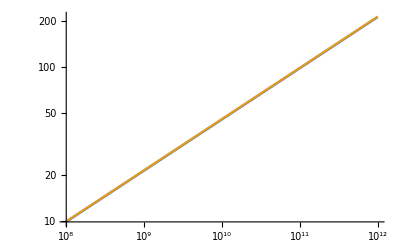

```mathematica
LogLogPlot[{r200FromM200[M200Msun,0],10^-1.67 M200Msun^(1/3)},{M200Msun,10^8,10^12}]
```

```mathematica
MsM200data=Table[{10^logM200,FindMsM200[10^logM200,0] 10^logM200},{logM200,8,14,0.05}];
M200FromMs=Interpolation[Reverse[MsM200dataᵀ]ᵀ];

FindM200FromMs[Ms_,Nσ_:0]:=Module[{logσ=0.15},M200FromMs[Ms] 10^(Nσ logσ)]

MsM200dataNσm1=Table[{10^logM200,FindMsM200[10^logM200,-1] 10^logM200},{logM200,8,14,0.05}];
M200FromMsNσm1=Interpolation[Reverse[MsM200dataNσm1ᵀ]ᵀ];

MsM200dataNσp1=Table[{10^logM200,FindMsM200[10^logM200,1] 10^logM200},{logM200,8,14,0.05}];
M200FromMsNσp1=Interpolation[Reverse[MsM200dataNσp1ᵀ]ᵀ];
```

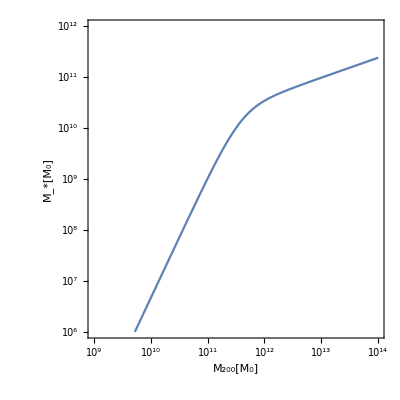
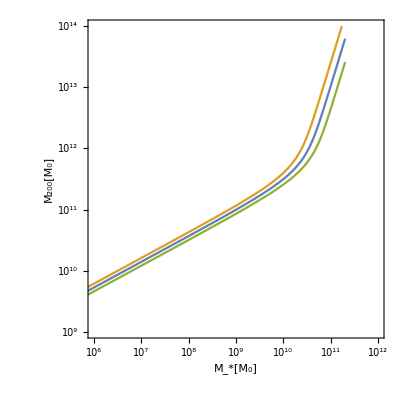

```mathematica
{LogLogPlot[FindMsM200[M200,0]M200,{M200,10^9,10^14},PlotRange->{{10^9,10^14},{10^6,10^12}},Evaluate@plotstyleSquare,FrameLabel->{{"M_*[M_0]",""},{"M_200[M_0]",""}}],LogLogPlot[{M200FromMs[Ms],M200FromMsNσm1[Ms],M200FromMsNσp1[Ms]},{Ms,100,2 10^11},PlotRange->{{10^6,10^12},{10^9,10^14}},Evaluate@plotstyleSquare,FrameLabel->{{"M_200[M_0]",""},{"M_*[M_0]",""}}]}
```

```mathematica
Clear[αxMsDC14];
αxMsDC14[MsMsun_,x200_,z_:0,Nσ_:0]:=Module[{A=0.025,M200Msun,ΔM200Msun,r200kpc,rskpc,Δrskpc,c200,Δc200,MsMhvir,ΔMsMhvir,αx,Δαx,ΣMspc2},
M200Msun=FindM200FromMs[MsMsun,0];
ΔM200Msun=Abs[FindM200FromMs[MsMsun,Nσ]-M200Msun];
r200kpc=r200FromM200[M200Msun,z];
rskpc=rsFromr200[r200kpc,0,A];
Δrskpc=Abs[rsFromr200[r200kpc,Nσ,A]-rskpc];
c200=c200Dutton[M200Msun,z,0];
Δc200=Abs[c200Dutton[M200Msun,z,Nσ]-c200];
MsMhvir=MsMsun/M200Msun;
ΔMsMhvir=(MsMsun ΔM200Msun)/M200Msun^2;

(*αx=αxDC14[x200,c200,MsMhvir];*)
{αx,Δαx}=αxDC14withErrors[x200,c200,Δc200,MsMhvir,ΔMsMhvir];
ΣMspc2=MsMsun/(π (10^3 rskpc)^2);

{ΣMspc2,αx,Δαx,rskpc,Δrskpc}
]
```

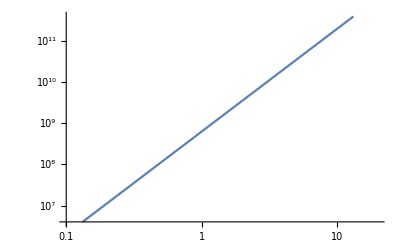

```mathematica
LogLogPlot[10^8.8 rs^2.5,{rs,0.1,20},PlotRange->{{0.1,20},{4 10^6,4 10^11}}]
```

```mathematica
Clear[rsSPARCkpc];
rsSPARCkpc[MsMsun_,Nσ_]:=Module[{logσ=0.25},(10^-8.8 MsMsun)^(1/2.5)10^(Nσ logσ)]

Clear[αxMsDC14SPARC];
αxMsDC14SPARC[MsMsun_,x200_,z_:0,Nσ_:0]:=Module[{A=0.025,M200Msun,ΔM200Msun,rskpc,Δrskpc,c200,Δc200,MsMhvir,ΔMsMhvir,αx,Δαx,ΣMspc2},
M200Msun=FindM200FromMs[MsMsun,0];
ΔM200Msun=Abs[FindM200FromMs[MsMsun,Nσ]-M200Msun];
rskpc=rsSPARCkpc[MsMsun,0];
Δrskpc=Abs[rsSPARCkpc[MsMsun,Nσ]-rskpc];
c200=c200Dutton[M200Msun,z,0];
Δc200=Abs[c200Dutton[M200Msun,z,Nσ]-c200];
MsMhvir=MsMsun/M200Msun;
ΔMsMhvir=(MsMsun ΔM200Msun)/M200Msun^2;

{αx,Δαx}=αxDC14withErrors[x200,c200,Δc200,MsMhvir,ΔMsMhvir];
ΣMspc2=MsMsun/(π (10^3 rskpc)^2);

{ΣMspc2,αx,Δαx,rskpc,Δrskpc}
]
```

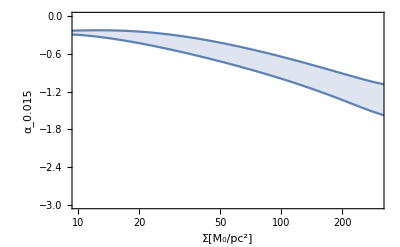
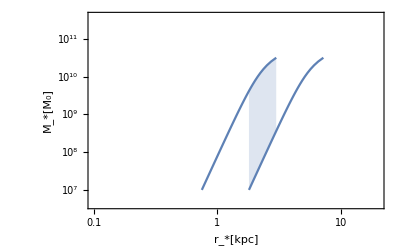
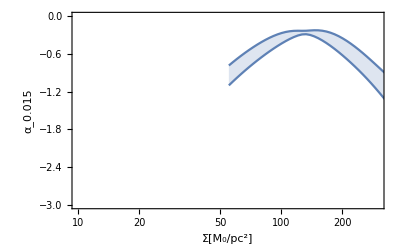
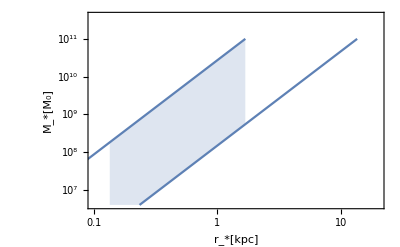
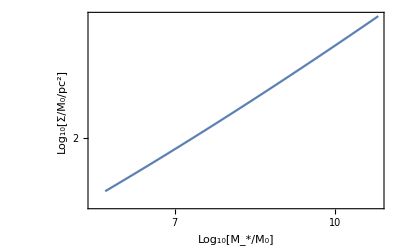

```mathematica
Module[{x=0.015,z=0},
Σαxdata=Table[Join[αxMsDC14[10^logMs,x,z,1],{10^logMs}],{logMs,7,10.5,0.1}];
ΣαxSPARCdata=Table[Join[αxMsDC14SPARC[10^logMs,x,z,1],{10^logMs}],{logMs,6,11,0.1}];

{ListLogLinearPlot[{{#[[1]],#[[2]]+#[[3]]}&/@Σαxdata,{#[[1]],#[[2]]-#[[3]]}&/@Σαxdata},Joined->True,PlotStyle->{{NiceColor[1]},{NiceColor[1]}},Filling->{1->{2}},PlotRange->{{10,3 10^2},{-3,0}},Evaluate@plotstyle,FrameLabel->{{"α_0.015",""},{"Σ[M_0/pc^2]",""}}],ListLogLogPlot[{{#[[4]]-#[[5]],#[[6]]}&/@Σαxdata,{#[[4]]+#[[5]],#[[6]]}&/@Σαxdata},Joined->True,PlotStyle->{{NiceColor[1]},{NiceColor[1]}},Filling->{1->{2}},PlotRange->{{0.1,2 10^1},{4 10^6,4 10^11}},Evaluate@plotstyle,FrameLabel->{{"M_*[M_0]",""},{"r_*[kpc]",""}}],ListLogLinearPlot[{{#[[1]],#[[2]]+#[[3]]}&/@ΣαxSPARCdata,{#[[1]],#[[2]]-#[[3]]}&/@ΣαxSPARCdata},Joined->True,PlotStyle->{{NiceColor[1]},{NiceColor[1]}},Filling->{1->{2}},PlotRange->{{10,3 10^2},{-3,0}},Evaluate@plotstyle,FrameLabel->{{"α_0.015",""},{"Σ[M_0/pc^2]",""}}],ListLogLogPlot[{{#[[4]]-#[[5]],#[[6]]}&/@ΣαxSPARCdata,{#[[4]]+#[[5]],#[[6]]}&/@ΣαxSPARCdata},Joined->True,PlotStyle->{{NiceColor[1]},{NiceColor[1]}},Filling->{1->{2}},PlotRange->{{0.1,2 10^1},{4 10^6,4 10^11}},Evaluate@plotstyle,FrameLabel->{{"M_*[M_0]",""},{"r_*[kpc]",""}}],
ListLogLogPlot[{{Log10[#[[6]]],Log10[#[[1]]]}&/@ΣαxSPARCdata},Joined->True,PlotStyle->{{NiceColor[1]},{NiceColor[1]}},(*PlotRange->{{0.1,2 10^1},{4 10^6,4 10^11}},*)Evaluate@plotstyle,FrameLabel->{{"Log_10[Σ/M_0/pc^2]",""},{"Log_10[M_*/M_0]",""}}]
}
]
```

```mathematica
(4 10^6)/(2π(10^3 0.2)^2)
```

15.9155

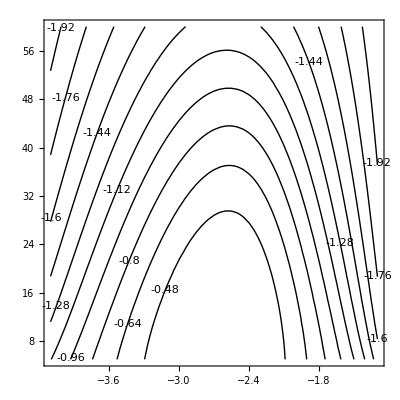

```mathematica
Module[{x=0.015},
ContourPlot[αxDC14[x,c200,10^logMsMhvir],{logMsMhvir,-4.1,-1.3},{c200,5,60},ContourShading->None,ContourLabels->All,Contours->10]]
```

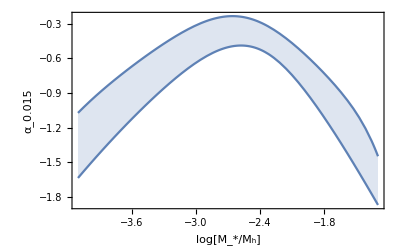
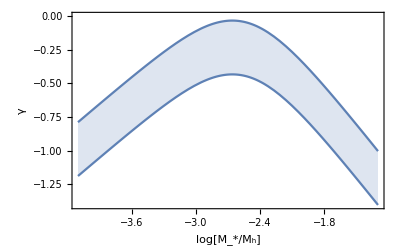

```mathematica
Module[{x200=0.015,c2001=3,c2002=30,γ},
γ=-(-0.06+Log10[(10^(X+2.56))^-0.68+10^(X+2.56)]);
{Plot[{αxDC14[x200,c2001,10^logMsMhvir],αxDC14[x200,c2002,10^logMsMhvir]},{logMsMhvir,-4.1,-1.3},Evaluate@plotstyle,FrameLabel->{{"α_0.015",""},{"log[M_*/M_h]",""}},PlotStyle->{{NiceColor[1]},{NiceColor[1]}},Filling->{1->{2}}],
Plot[{γ-0.2,γ+0.2},{X,-4.1,-1.3},Evaluate@plotstyle,FrameLabel->{{"γ",""},{"log[M_*/M_h]",""}},PlotStyle->{{NiceColor[1]},{NiceColor[1]}},Filling->{1->{2}}]
}]
```